```mathematica
Remove["Global`*"]
(*<<PhysicalConstants *)
<<Units`
(*<<VectorAnalysis`*)
<<FourierSeries`
(*<<LinearRegression`*)
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
(*Proton in B11*)
EtPR[x_]=-4038.621695160617+30.217944902944236/(0.007481857100785539+3.2469601381813174*^-7 ⅇ^(-37.49736075902206 x))+3.307130653753605 x+1515.3152978046726 x^1.9990033267320544-1506.2506067955821 x^2+0.09463470541261623 x^3-0.13448967381673807 x^4+0.047932270219233936 x^5-0.005179352017528617 x^6;(*MeV to µm*)
PRtE= InverseFunction[EtPR[#]&];

(*1/(Stopping Power MeV/μm)*)
f[x_]=(4.419276392445275+ⅇ^(-7.3803552653244 (-0.10066107776724603+x))-0.5673657094346726/(1+0.7297860911389368 (-1.1106115256038274+x)^2)+0.5758738282552386/(1+1.030347643016361 (-0.9802921157540312+x)^3)+9.861753173526887 x-0.06433184715293583( x)^2+3.8810193819415244 Log[4.15270754026916 Abs[0.04038187709701176+x]]);

(* Cross Section Units: barns.  1 b = 10^-16 µm^2 *)
(*g[x_]=10^-16((.000002)/((x-.155)^2+.00005)+0.4*(Erf[(x-0.3)/(.06)]+1)*(.022)/((x-.63)^2+(0.3/2)^2)+(.012)/((x-1.4)^2+.1)+(.01)/((x-2.65)^2+.06)+0.03*(Erf[(x-1.2)/(.21)]+1));*)
g[x_]=10^-3*10^-16*(-3.5650236274749614+23.20200042365487/(0.045773195674098134+(-2.5808801675740694+x)^2)+4.287083868050379/(0.04657872865678219+(-1.4379138393368533+x)^2)+710883.2810500122/(-2.8453995938152443*^10+(7.167293360108095*^7+x)^2)-(36418.14230130918 (1+Erf[7.4769146951401755 (-0.7308497211376067+x)]))/(30.42724516180452+(-2.2968820148661604+x)^2)+1282.7470938628087 (1+Erf[4.493328010602532 (-0.5676324141957634+x)]));(*new cross section*)
(* Peak of Cross Section/Stopping Power*)
PeakPR=EtPR[0.6425599979725697];(*MeV to µm*)
```

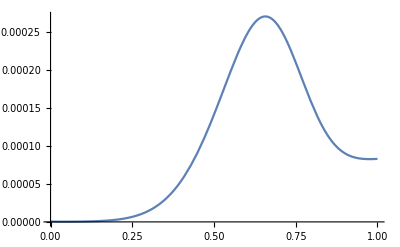

```mathematica
Plot[(6.022141×10^23)/10.81*2.3502/10^12*f[x]*g[x],{x,0,1}]
```

```mathematica
thickeness = 0.1 ;(*µm*)(*Thickness of Lebow Foil*)
```

```mathematica
PeakBins=50;
Start=If[PeakPR-thickeness<0,0,PeakPR-thickeness];
Stepsize=(PeakPR-Start)/(PeakBins-1);
IntN=Range[PeakBins];
```

```mathematica
(*Find the Energies to get max alphas*)
For[i=1,i≤PeakBins,i++,
minE=If[Start+(i-1)Stepsize≥EtPR[0],PRtE[Start+(i-1)Stepsize],0];
maxE=If[Start+(i-1)Stepsize+thickeness≥EtPR[0],PRtE[Start+(i-1)Stepsize+thickeness],0];
minE=If[minE<0∨minE>maxE∨Im[minE]≠0,0,minE];
maxE=If[maxE<0∨minE>maxE∨Im[maxE]≠0,0,maxE];
(*Compare all integration of different energies in array for number of alphas generated*)
IntN[[i]]=NIntegrate[f[x]*g[x],{x,minE,maxE}];
	]; 
(*Max[IntN];*)
(* What position was minE and maxE for the max integration *)
Pos=Position[IntN,Max[IntN]][[1,1]];
minE=If[Start+(Pos-1)Stepsize≥EtPR[0],PRtE[Start+(Pos-1)Stepsize],0];
maxE=If[Start+(Pos-1)Stepsize+thickeness≥EtPR[0],PRtE[Start+(Pos-1)Stepsize+thickeness],0];
minE=If[minE<0∨minE>maxE∨Im[minE]≠0,0,minE];
maxE=If[maxE<0∨minE>maxE∨Im[maxE]≠0,0,maxE];
```

```mathematica
maxE
```

0.643247

```mathematica
minE
```

0.636497

```mathematica
Int = (6.022141×10^23)/10.81*2.3502/10^12*NIntegrate[f[x]*g[x],{x,minE,maxE}]
```

1.80779×10^-6

```mathematica
1/Int
```

553161.

```mathematica
EtPR[maxE] - EtPR[minE]
```

0.1

```mathematica
m1/(√(2m*Q))√((2 Ei)/M)
```

(√(Ei/M) m1)/(√(m Q))

```mathematica
m1/(√(2(m1*m2)/(m1+m2)*Q))√((2 Ei)/M)
```

(√(Ei/M) m1)/(√((m1 m2 Q)/(m1+m2)))